```mathematica
Задача №1
```

Задача №1

```mathematica
equation1 = -1/(2m)u''[r] +(l(l+1))/(2m*r^2)u[r]-e^2/(ℏ^2 r)u[r]-En/ℏ^2 u[r];
```

```mathematica
equation = -3.80998(u''[r]-(l(l+1))/r^2 u[r])-14.398 u[r]/r+0.8504*u[r]; (*n = 4, все коэффициенты в электронвольтах*)
```

```mathematica
sol0:=NDSolveValue[{(equation==0)/.{l->0},u[10^-2]==0,u'[10^-2]==1},u,{r,10^-2,25}]
```

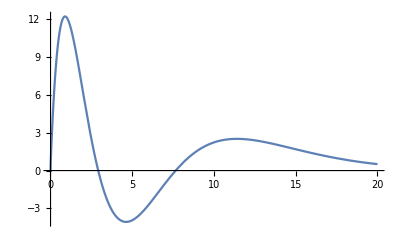

```mathematica
Plot[{sol0[x] / x},{x, 10^-2,20}]
```

```mathematica
sol1:=NDSolveValue[{(equation==0)/.{l->3},u[10^-2]==0,u'[10^-2]==0.01},u,{r,10^-2,25}]
```

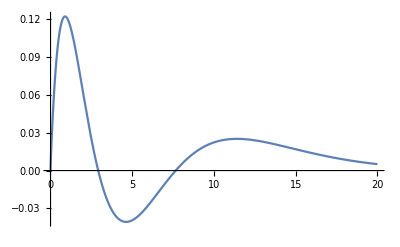

SetDelayed::write: Tag Integer in 1[x_] is Protected.

```mathematica
Plot[{sol1[x] / x},{x, 10^-2,20}]
```

```mathematica
Задача №3
```

Задача №3

```mathematica
D[(Задача №3), Задача]
```

№3

```mathematica
ClearAll[i]
ClearAll[j]
ClearAll[k]
ClearAll[NonCommutativeMultiply]
```

```mathematica
Unprotect[NonCommutativeMultiply]
NonCommutativeMultiply[a_]:=a
NonCommutativeMultiply[a___,n_?NumericQ,b___]:=n a**b
NonCommutativeMultiply[a___,n_?NumericQ*b___]:=n a**b
NonCommutativeMultiply[n_?NumericQ*a___,b___]:=n a**b
NonCommutativeMultiply[]:=1
```

{}

```mathematica
NonCommutativeMultiply[i, i] := -1
NonCommutativeMultiply[j, j] := -1
NonCommutativeMultiply[k, k] := -1
```

```mathematica
NonCommutativeMultiply[i, j] := k
```

```mathematica
NonCommutativeMultiply[j, i] := - k
```

```mathematica
NonCommutativeMultiply[j, i]
```

-k

```mathematica
NonCommutativeMultiply[j, k] := i
NonCommutativeMultiply[k, j] := -i
```

```mathematica
NonCommutativeMultiply[k, i] := j
```

```mathematica
NonCommutativeMultiply[i, k] := -j
```

```mathematica
Distribute[(1+j)**(2 + i)]
```

2+i+2 j-k

```mathematica
2+i+2 j-k
1**2
```

2+i+2 j-k

2

```mathematica
quat1 = 1 + i -9**j + k
quat2 = -2 -i + j + 3**k
```

1+i-9 j+k

-2-i+j+3 k

```mathematica
quat1 + quat2
```

-1-8 j+4 k

```mathematica
Distribute[quat1**quat2]
```

5-31 i+15 j-7 k

```mathematica
23**i**14**j
```

322 k ^2

```mathematica
Задача №4
```

Задача №4

```mathematica
Clear[n, i, H];
HamEq[H_,coord_]:=
Block[{n,i,equations,H1, H2},
n=Length[coord];
equations=Table[0,n];
For[i=1,i≤n,i += 2,
	H1 = D[H, coord[[i+1]][t]] ;
equations[[i]]= D[coord[[i]][t],t]-H1 ;
];
	For[i=2,i≤n,i += 2,
	H2 = D[H, coord[[i-1]][t]];
	equations[[i]]= D[coord[[i]][t],t]+ H2;
	];
	Return[equations]
	];
```

```mathematica
H=p1[t]^2/(2m1)+ p2[t]^2/(2m2) +  U[q1[t]] + U[q2[t]] + Uint[q1[t] - q2[t]];
```

```mathematica
HamEq[H,{q1,p1, q2, p2}]
```

{-p1[t]/m1+q1'[t],p1'[t]+U'[q1[t]]+Uint'[q1[t]-q2[t]],-p2[t]/m2+q2'[t],p2'[t]+U'[q2[t]]-Uint'[q1[t]-q2[t]]}

```mathematica
Задача №5
```

Задача №5

```mathematica
Clear[n, i, H];
HamJacEq[H_,coord_]:=
Block[{n,i,equation,S0,S1, rule, rule1, rule0},
n=Length[coord];
S0=StringRiffle[Table[coord[[i]],{i,1,n, 2}],","];
S1=ToExpression["S["<>S0<>",t]"];
rule0 = Table[coord[[i]][t]->coord[[i]],{i,1,n}];
rule  = Table[coord[[i]]->D[S1,coord[[i-1]]],{i,2,n, 2}];
rule1=Table[coord[[i]]->coord[[i]][t],{i,1, n,2}];
equation = H /. rule0 /. rule;
equation = equation + D[S1, t];
Return[equation /.rule1]
];
H=p1[t]^2/(2m1)+ p2[t]^2/(2m2) +  U[q1[t]] + U[q2[t]] + Uint[q1[t] - q2[t]];
```

```mathematica
HamJacEq[H,{q1,p1, q2, p2}]
```

U[q1[t]]+U[q2[t]]+Uint[q1[t]-q2[t]]+S^(0,0,1)[q1[t],q2[t],t]+((S^(0,1,0)[q1[t],q2[t],t])^2)/(2 m2)+((S^(1,0,0)[q1[t],q2[t],t])^2)/(2 m1)